```mathematica
Zero[J_,q_,l_]:=Re[(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))]
```

```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jone_,Jtwo_,p_,z_] := 1+ 2*IntPlus[1,Jone,Jtwo,p,z]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_,Jone_,p_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Jone,Xstart,p,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
a= Check[FindRoot[NullsHolm[Jone,Jtwoo,p,z]==0,{z,z/.lst[[n,2]]}
],z->0];
AppendTo[lst,{Jtwoo,a}];
,{n,1,199,1}
];
lst
]
```

```mathematica
ListerGreaterRange[Plusminus_,Xstart_,StartIteration_,Jone_,p_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Jone,Xstart,p,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
a= Check[FindRoot[NullsHolm[Jone,Jtwoo,p,z]==0,{z,z/.lst[[n,2]]}
],z->0];
AppendTo[lst,{Jtwoo,a}];
,{n,1,399,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
modulerGreaterRange[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,400,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,400,1}];
lst
]
```

```mathematica
Verlauf[HowMany_,p_] := 
Module[{lst={}},
For[i=1,i<HowMany+1,i++,
AppendTo[lst,{1,i*0.1,p}];
AppendTo[lst,Fueger[moduler[Lister[-1,-0.0005,Zero[1,i*0.1,p],i*0.1,p]],modulerGreaterRange[ListerGreaterRange[1,0.0005,Zero[1,i*0.1,p],i*0.1,p]]]];
];
l=lst
]
```

```mathematica
Verlauf[3,0.6]
```

{{1,0.1,0.6},{{-0.0005,0.758091},{-0.001,0.757892},{-0.0015,0.757692},{-0.002,0.757489},{-0.0025,0.757285},{-0.003,0.757079},{-0.0035,0.756871},{-0.004,0.756661},{-0.0045,0.756449},{-0.005,0.756235},{-0.0055,0.75602},{-0.006,0.755802},{-0.0065,0.755583},{-0.007,0.755362},{-0.0075,0.755139},{-0.008,0.754914},{-0.0085,0.754687},{-0.009,0.754459},{-0.0095,0.754228},{-0.01,0.753996},{-0.0105,0.753762},{-0.011,0.753526},{-0.0115,0.753289},{-0.012,0.753049},{-0.0125,0.752808},{-0.013,0.752565},{-0.0135,0.75232},{-0.014,0.752073},{-0.0145,0.751824},{-0.015,0.751574},{-0.0155,0.751322},{-0.016,0.751068},{-0.0165,0.750812},{-0.017,0.750555},{-0.0175,0.750296},{-0.018,0.750034},{-0.0185,0.749772},{-0.019,0.749507},{-0.0195,0.749241},{-0.02,0.748973},{-0.0205,0.748703},{-0.021,0.748431},{-0.0215,0.748158},{-0.022,0.747883},{-0.0225,0.747606},{-0.023,0.747327},{-0.0235,0.747047},{-0.024,0.746765},{-0.0245,0.746481},{-0.025,0.746196},{-0.0255,0.745909},{-0.026,0.74562},{-0.0265,0.745329},{-0.027,0.745037},{-0.0275,0.744743},{-0.028,0.744447},{-0.0285,0.74415},{-0.029,0.743851},{-0.0295,0.74355},{-0.03,0.743248},{-0.0305,0.742944},{-0.031,0.742638},{-0.0315,0.742331},{-0.032,0.742022},{-0.0325,0.741711},{-0.033,0.741398},{-0.0335,0.741084},{-0.034,0.740769},{-0.0345,0.740451},{-0.035,0.740132},{-0.0355,0.739812},{-0.036,0.73949},{-0.0365,0.739166},{-0.037,0.73884},{-0.0375,0.738513},{-0.038,0.738184},{-0.0385,0.737854},{-0.039,0.737522},{-0.0395,0.737189},{-0.04,0.736853},{-0.0405,0.736517},{-0.041,0.736178},{-0.0415,0.735838},{-0.042,0.735497},{-0.0425,0.735154},{-0.043,0.734809},{-0.0435,0.734463},{-0.044,0.734115},{-0.0445,0.733766},{-0.045,0.733415},{-0.0455,0.733062},{-0.046,0.732708},{-0.0465,0.732353},{-0.047,0.731995},{-0.0475,0.731637},{-0.048,0.731277},{-0.0485,0.730915},{-0.049,0.730551},{-0.0495,0.730187},{-0.05,0.72982},{-0.0505,0.729452},{-0.051,0.729083},{-0.0515,0.728712},{-0.052,0.72834},{-0.0525,0.727966},{-0.053,0.72759},{-0.0535,0.727213},{-0.054,0.726835},{-0.0545,0.726455},{-0.055,0.726073},{-0.0555,0.72569},{-0.056,0.725306},{-0.0565,0.72492},{-0.057,0.724533},{-0.0575,0.724144},{-0.058,0.723754},{-0.0585,0.723362},{-0.059,0.722969},{-0.0595,0.722574},{-0.06,0.722178},{-0.0605,0.72178},{-0.061,0.721381},{-0.0615,0.72098},{-0.062,0.720578},{-0.0625,0.720175},{-0.063,0.71977},{-0.0635,0.719364},{-0.064,0.718956},{-0.0645,0.718547},{-0.065,0.718136},{-0.0655,0.717724},{-0.066,0.717311},{-0.0665,0.716896},{-0.067,0.71648},{-0.0675,0.716062},{-0.068,0.715643},{-0.0685,0.715223},{-0.069,0.714801},{-0.0695,0.714377},{-0.07,0.713953},{-0.0705,0.713527},{-0.071,0.713099},{-0.0715,0.71267},{-0.072,0.71224},{-0.0725,0.711808},{-0.073,0.711375},{-0.0735,0.710941},{-0.074,0.710505},{-0.0745,0.710068},{-0.075,0.709629},{-0.0755,0.709189},{-0.076,0.708748},{-0.0765,0.708306},{-0.077,0.707862},{-0.0775,0.707416},{-0.078,0.70697},{-0.0785,0.706522},{-0.079,0.706072},{-0.0795,0.705621},{-0.08,0.705169},{-0.0805,0.704716},{-0.081,0.704261},{-0.0815,0.703805},{-0.082,0.703348},{-0.0825,0.702889},{-0.083,0.702429},{-0.0835,0.701967},{-0.084,0.701504},{-0.0845,0.70104},{-0.085,0.700575},{-0.0855,0.700108},{-0.086,0.69964},{-0.0865,0.699171},{-0.087,0.6987},{-0.0875,0.698228},{-0.088,0.697755},{-0.0885,0.69728},{-0.089,0.696804},{-0.0895,0.696327},{-0.09,0.695849},{-0.0905,0.695369},{-0.091,0.694888},{-0.0915,0.694405},{-0.092,0.693922},{-0.0925,0.693437},{-0.093,0.69295},{-0.0935,0.692463},{-0.094,0.691974},{-0.0945,0.691484},{-0.095,0.690993},{-0.0955,0.6905},{-0.096,0.690006},{-0.0965,0.689511},{-0.097,0.689014},{-0.0975,0.688516},{-0.098,0.688017},{-0.0985,0.687517},{-0.099,0.687015},{-0.0995,0.686513},{-0.1,0.686008},{0.0005,0.758482},{0.001,0.758675},{0.0015,0.758866},{0.002,0.759055},{0.0025,0.759242},{0.003,0.759428},{0.0035,0.759611},{0.004,0.759792},{0.0045,0.759972},{0.005,0.760149},{0.0055,0.760325},{0.006,0.760498},{0.0065,0.76067},{0.007,0.76084},{0.0075,0.761008},{0.008,0.761173},{0.0085,0.761337},{0.009,0.761499},{0.0095,0.761659},{0.01,0.761817},{0.0105,0.761973},{0.011,0.762127},{0.0115,0.762279},{0.012,0.762429},{0.0125,0.762577},{0.013,0.762723},{0.0135,0.762867},{0.014,0.76301},{0.0145,0.76315},{0.015,0.763288},{0.0155,0.763424},{0.016,0.763558},{0.0165,0.76369},{0.017,0.76382},{0.0175,0.763948},{0.018,0.764074},{0.0185,0.764198},{0.019,0.764321},{0.0195,0.764441},{0.02,0.764559},{0.0205,0.764675},{0.021,0.764788},{0.0215,0.7649},{0.022,0.76501},{0.0225,0.765118},{0.023,0.765224},{0.0235,0.765328},{0.024,0.765429},{0.0245,0.765529},{0.025,0.765627},{0.0255,0.765722},{0.026,0.765816},{0.0265,0.765907},{0.027,0.765997},{0.0275,0.766084},{0.028,0.76617},{0.0285,0.766253},{0.029,0.766334},{0.0295,0.766413},{0.03,0.76649},{0.0305,0.766565},{0.031,0.766638},{0.0315,0.766709},{0.032,0.766778},{0.0325,0.766845},{0.033,0.766909},{0.0335,0.766972},{0.034,0.767033},{0.0345,0.767091},{0.035,0.767147},{0.0355,0.767202},{0.036,0.767254},{0.0365,0.767304},{0.037,0.767352},{0.0375,0.767398},{0.038,0.767442},{0.0385,0.767484},{0.039,0.767523},{0.0395,0.767561},{0.04,0.767597},{0.0405,0.76763},{0.041,0.767661},{0.0415,0.767691},{0.042,0.767718},{0.0425,0.767743},{0.043,0.767766},{0.0435,0.767787},{0.044,0.767806},{0.0445,0.767822},{0.045,0.767837},{0.0455,0.76785},{0.046,0.76786},{0.0465,0.767868},{0.047,0.767875},{0.0475,0.767879},{0.048,0.767881},{0.0485,0.767881},{0.049,0.767879},{0.0495,0.767875},{0.05,0.767868},{0.0505,0.76786},{0.051,0.767849},{0.0515,0.767837},{0.052,0.767822},{0.0525,0.767805},{0.053,0.767787},{0.0535,0.767766},{0.054,0.767743},{0.0545,0.767718},{0.055,0.76769},{0.0555,0.767661},{0.056,0.76763},{0.0565,0.767596},{0.057,0.767561},{0.0575,0.767523},{0.058,0.767483},{0.0585,0.767442},{0.059,0.767398},{0.0595,0.767352},{0.06,0.767304},{0.0605,0.767254},{0.061,0.767201},{0.0615,0.767147},{0.062,0.767091},{0.0625,0.767033},{0.063,0.766972},{0.0635,0.76691},{0.064,0.766845},{0.0645,0.766778},{0.065,0.766709},{0.0655,0.766639},{0.066,0.766566},{0.0665,0.766491},{0.067,0.766414},{0.0675,0.766335},{0.068,0.766254},{0.0685,0.766171},{0.069,0.766085},{0.0695,0.765998},{0.07,0.765909},{0.0705,0.765818},{0.071,0.765724},{0.0715,0.765629},{0.072,0.765531},{0.0725,0.765432},{0.073,0.76533},{0.0735,0.765227},{0.074,0.765121},{0.0745,0.765014},{0.075,0.764904},{0.0755,0.764792},{0.076,0.764679},{0.0765,0.764563},{0.077,0.764445},{0.0775,0.764325},{0.078,0.764204},{0.0785,0.76408},{0.079,0.763954},{0.0795,0.763826},{0.08,0.763697},{0.0805,0.763565},{0.081,0.763431},{0.0815,0.763296},{0.082,0.763158},{0.0825,0.763018},{0.083,0.762876},{0.0835,0.762733},{0.084,0.762587},{0.0845,0.76244},{0.085,0.76229},{0.0855,0.762138},{0.086,0.761985},{0.0865,0.761829},{0.087,0.761672},{0.0875,0.761513},{0.088,0.761351},{0.0885,0.761188},{0.089,0.761023},{0.0895,0.760856},{0.09,0.760686},{0.0905,0.760515},{0.091,0.760342},{0.0915,0.760168},{0.092,0.759991},{0.0925,0.759812},{0.093,0.759631},{0.0935,0.759449},{0.094,0.759264},{0.0945,0.759078},{0.095,0.75889},{0.0955,0.758699},{0.096,0.758507},{0.0965,0.758313},{0.097,0.758117},{0.0975,0.75792},{0.098,0.75772},{0.0985,0.757519},{0.099,0.757315},{0.0995,0.75711},{0.1,0.756903},{0.1005,0.756694},{0.101,0.756483},{0.1015,0.75627},{0.102,0.756056},{0.1025,0.755839},{0.103,0.755621},{0.1035,0.755401},{0.104,0.755179},{0.1045,0.754955},{0.105,0.754729},{0.1055,0.754502},{0.106,0.754273},{0.1065,0.754042},{0.107,0.753809},{0.1075,0.753574},{0.108,0.753338},{0.1085,0.753099},{0.109,0.752859},{0.1095,0.752617},{0.11,0.752374},{0.1105,0.752128},{0.111,0.751881},{0.1115,0.751632},{0.112,0.751381},{0.1125,0.751128},{0.113,0.750874},{0.1135,0.750618},{0.114,0.75036},{0.1145,0.7501},{0.115,0.749839},{0.1155,0.749576},{0.116,0.749311},{0.1165,0.749044},{0.117,0.748776},{0.1175,0.748506},{0.118,0.748234},{0.1185,0.74796},{0.119,0.747685},{0.1195,0.747408},{0.12,0.74713},{0.1205,0.746849},{0.121,0.746567},{0.1215,0.746283},{0.122,0.745998},{0.1225,0.745711},{0.123,0.745422},{0.1235,0.745131},{0.124,0.744839},{0.1245,0.744545},{0.125,0.744249},{0.1255,0.743952},{0.126,0.743653},{0.1265,0.743353},{0.127,0.74305},{0.1275,0.742746},{0.128,0.742441},{0.1285,0.742134},{0.129,0.741825},{0.1295,0.741514},{0.13,0.741202},{0.1305,0.740889},{0.131,0.740573},{0.1315,0.740256},{0.132,0.739938},{0.1325,0.739617},{0.133,0.739296},{0.1335,0.738972},{0.134,0.738647},{0.1345,0.738321},{0.135,0.737992},{0.1355,0.737663},{0.136,0.737331},{0.1365,0.736998},{0.137,0.736664},{0.1375,0.736327},{0.138,0.73599},{0.1385,0.73565},{0.139,0.73531},{0.1395,0.734967},{0.14,0.734623},{0.1405,0.734278},{0.141,0.733931},{0.1415,0.733582},{0.142,0.733232},{0.1425,0.73288},{0.143,0.732527},{0.1435,0.732172},{0.144,0.731816},{0.1445,0.731458},{0.145,0.731099},{0.1455,0.730738},{0.146,0.730376},{0.1465,0.730012},{0.147,0.729646},{0.1475,0.729279},{0.148,0.728911},{0.1485,0.728541},{0.149,0.72817},{0.1495,0.727797},{0.15,0.727423},{0.1505,0.727047},{0.151,0.726669},{0.1515,0.726291},{0.152,0.72591},{0.1525,0.725529},{0.153,0.725145},{0.1535,0.724761},{0.154,0.724375},{0.1545,0.723987},{0.155,0.723598},{0.1555,0.723208},{0.156,0.722816},{0.1565,0.722422},{0.157,0.722027},{0.1575,0.721631},{0.158,0.721233},{0.1585,0.720834},{0.159,0.720434},{0.1595,0.720032},{0.16,0.719628},{0.1605,0.719224},{0.161,0.718817},{0.1615,0.71841},{0.162,0.718001},{0.1625,0.71759},{0.163,0.717178},{0.1635,0.716765},{0.164,0.71635},{0.1645,0.715934},{0.165,0.715517},{0.1655,0.715098},{0.166,0.714678},{0.1665,0.714256},{0.167,0.713833},{0.1675,0.713409},{0.168,0.712983},{0.1685,0.712556},{0.169,0.712128},{0.1695,0.711698},{0.17,0.711267},{0.1705,0.710834},{0.171,0.7104},{0.1715,0.709965},{0.172,0.709528},{0.1725,0.70909},{0.173,0.708651},{0.1735,0.70821},{0.174,0.707768},{0.1745,0.707325},{0.175,0.70688},{0.1755,0.706434},{0.176,0.705986},{0.1765,0.705538},{0.177,0.705088},{0.1775,0.704636},{0.178,0.704184},{0.1785,0.70373},{0.179,0.703274},{0.1795,0.702818},{0.18,0.70236},{0.1805,0.7019},{0.181,0.70144},{0.1815,0.700978},{0.182,0.700515},{0.1825,0.70005},{0.183,0.699584},{0.1835,0.699117},{0.184,0.698649},{0.1845,0.698179},{0.185,0.697708},{0.1855,0.697236},{0.186,0.696762},{0.1865,0.696287},{0.187,0.695811},{0.1875,0.695333},{0.188,0.694855},{0.1885,0.694375},{0.189,0.693893},{0.1895,0.693411},{0.19,0.692927},{0.1905,0.692442},{0.191,0.691955},{0.1915,0.691468},{0.192,0.690979},{0.1925,0.690489},{0.193,0.689997},{0.1935,0.689504},{0.194,0.68901},{0.1945,0.688515},{0.195,0.688019},{0.1955,0.687521},{0.196,0.687022},{0.1965,0.686522},{0.197,0.68602},{0.1975,0.685517},{0.198,0.685013},{0.1985,0.684508},{0.199,0.684001},{0.1995,0.683494},{0.2,0.682985}},{1,0.2,0.6},{{-0.0005,0.64769},{-0.001,0.647305},{-0.0015,0.646918},{-0.002,0.646529},{-0.0025,0.646138},{-0.003,0.645746},{-0.0035,0.645351},{-0.004,0.644955},{-0.0045,0.644557},{-0.005,0.644158},{-0.0055,0.643756},{-0.006,0.643353},{-0.0065,0.642948},{-0.007,0.642541},{-0.0075,0.642133},{-0.008,0.641722},{-0.0085,0.64131},{-0.009,0.640897},{-0.0095,0.640481},{-0.01,0.640064},{-0.0105,0.639645},{-0.011,0.639224},{-0.0115,0.638801},{-0.012,0.638377},{-0.0125,0.637951},{-0.013,0.637523},{-0.0135,0.637094},{-0.014,0.636663},{-0.0145,0.63623},{-0.015,0.635795},{-0.0155,0.635359},{-0.016,0.634921},{-0.0165,0.634481},{-0.017,0.634039},{-0.0175,0.633596},{-0.018,0.633151},{-0.0185,0.632704},{-0.019,0.632256},{-0.0195,0.631806},{-0.02,0.631354},{-0.0205,0.630901},{-0.021,0.630445},{-0.0215,0.629989},{-0.022,0.62953},{-0.0225,0.62907},{-0.023,0.628608},{-0.0235,0.628144},{-0.024,0.627679},{-0.0245,0.627212},{-0.025,0.626743},{-0.0255,0.626273},{-0.026,0.625801},{-0.0265,0.625327},{-0.027,0.624852},{-0.0275,0.624375},{-0.028,0.623896},{-0.0285,0.623416},{-0.029,0.622934},{-0.0295,0.62245},{-0.03,0.621965},{-0.0305,0.621478},{-0.031,0.620989},{-0.0315,0.620499},{-0.032,0.620007},{-0.0325,0.619513},{-0.033,0.619018},{-0.0335,0.618521},{-0.034,0.618022},{-0.0345,0.617522},{-0.035,0.61702},{-0.0355,0.616517},{-0.036,0.616011},{-0.0365,0.615505},{-0.037,0.614996},{-0.0375,0.614486},{-0.038,0.613974},{-0.0385,0.613461},{-0.039,0.612946},{-0.0395,0.612429},{-0.04,0.611911},{-0.0405,0.611391},{-0.041,0.61087},{-0.0415,0.610347},{-0.042,0.609822},{-0.0425,0.609296},{-0.043,0.608768},{-0.0435,0.608238},{-0.044,0.607707},{-0.0445,0.607174},{-0.045,0.60664},{-0.0455,0.606103},{-0.046,0.605566},{-0.0465,0.605026},{-0.047,0.604486},{-0.0475,0.603943},{-0.048,0.603399},{-0.0485,0.602853},{-0.049,0.602306},{-0.0495,0.601757},{-0.05,0.601206},{-0.0505,0.600654},{-0.051,0.6001},{-0.0515,0.599545},{-0.052,0.598988},{-0.0525,0.598429},{-0.053,0.597869},{-0.0535,0.597307},{-0.054,0.596743},{-0.0545,0.596178},{-0.055,0.595612},{-0.0555,0.595043},{-0.056,0.594473},{-0.0565,0.593902},{-0.057,0.593329},{-0.0575,0.592754},{-0.058,0.592178},{-0.0585,0.5916},{-0.059,0.59102},{-0.0595,0.590439},{-0.06,0.589857},{-0.0605,0.589272},{-0.061,0.588686},{-0.0615,0.588099},{-0.062,0.58751},{-0.0625,0.586919},{-0.063,0.586327},{-0.0635,0.585733},{-0.064,0.585137},{-0.0645,0.58454},{-0.065,0.583941},{-0.0655,0.583341},{-0.066,0.582739},{-0.0665,0.582135},{-0.067,0.58153},{-0.0675,0.580923},{-0.068,0.580315},{-0.0685,0.579705},{-0.069,0.579093},{-0.0695,0.57848},{-0.07,0.577865},{-0.0705,0.577249},{-0.071,0.576631},{-0.0715,0.576011},{-0.072,0.57539},{-0.0725,0.574767},{-0.073,0.574143},{-0.0735,0.573517},{-0.074,0.572889},{-0.0745,0.572259},{-0.075,0.571629},{-0.0755,0.570996},{-0.076,0.570362},{-0.0765,0.569726},{-0.077,0.569089},{-0.0775,0.568449},{-0.078,0.567809},{-0.0785,0.567166},{-0.079,0.566523},{-0.0795,0.565877},{-0.08,0.56523},{-0.0805,0.564581},{-0.081,0.56393},{-0.0815,0.563278},{-0.082,0.562625},{-0.0825,0.561969},{-0.083,0.561312},{-0.0835,0.560654},{-0.084,0.559993},{-0.0845,0.559331},{-0.085,0.558668},{-0.0855,0.558003},{-0.086,0.557336},{-0.0865,0.556667},{-0.087,0.555997},{-0.0875,0.555325},{-0.088,0.554652},{-0.0885,0.553976},{-0.089,0.5533},{-0.0895,0.552621},{-0.09,0.551941},{-0.0905,0.551259},{-0.091,0.550576},{-0.0915,0.549891},{-0.092,0.549204},{-0.0925,0.548515},{-0.093,0.547825},{-0.0935,0.547133},{-0.094,0.54644},{-0.0945,0.545744},{-0.095,0.545047},{-0.0955,0.544349},{-0.096,0.543648},{-0.0965,0.542946},{-0.097,0.542243},{-0.0975,0.541537},{-0.098,0.54083},{-0.0985,0.540121},{-0.099,0.53941},{-0.0995,0.538698},{-0.1,0.537984},{0.0005,0.648456},{0.001,0.648836},{0.0015,0.649214},{0.002,0.64959},{0.0025,0.649965},{0.003,0.650338},{0.0035,0.650708},{0.004,0.651077},{0.0045,0.651445},{0.005,0.65181},{0.0055,0.652174},{0.006,0.652535},{0.0065,0.652895},{0.007,0.653253},{0.0075,0.65361},{0.008,0.653964},{0.0085,0.654316},{0.009,0.654667},{0.0095,0.655016},{0.01,0.655363},{0.0105,0.655708},{0.011,0.656051},{0.0115,0.656392},{0.012,0.656732},{0.0125,0.657069},{0.013,0.657405},{0.0135,0.657739},{0.014,0.658071},{0.0145,0.658401},{0.015,0.658729},{0.0155,0.659055},{0.016,0.65938},{0.0165,0.659702},{0.017,0.660023},{0.0175,0.660341},{0.018,0.660658},{0.0185,0.660973},{0.019,0.661286},{0.0195,0.661597},{0.02,0.661906},{0.0205,0.662213},{0.021,0.662518},{0.0215,0.662821},{0.022,0.663122},{0.0225,0.663422},{0.023,0.663719},{0.0235,0.664015},{0.024,0.664308},{0.0245,0.6646},{0.025,0.664889},{0.0255,0.665177},{0.026,0.665463},{0.0265,0.665747},{0.027,0.666028},{0.0275,0.666308},{0.028,0.666586},{0.0285,0.666862},{0.029,0.667136},{0.0295,0.667407},{0.03,0.667677},{0.0305,0.667945},{0.031,0.668211},{0.0315,0.668475},{0.032,0.668737},{0.0325,0.668997},{0.033,0.669255},{0.0335,0.66951},{0.034,0.669764},{0.0345,0.670016},{0.035,0.670266},{0.0355,0.670514},{0.036,0.670759},{0.0365,0.671003},{0.037,0.671245},{0.0375,0.671485},{0.038,0.671722},{0.0385,0.671958},{0.039,0.672191},{0.0395,0.672423},{0.04,0.672652},{0.0405,0.67288},{0.041,0.673105},{0.0415,0.673328},{0.042,0.673549},{0.0425,0.673769},{0.043,0.673986},{0.0435,0.674201},{0.044,0.674414},{0.0445,0.674625},{0.045,0.674833},{0.0455,0.67504},{0.046,0.675245},{0.0465,0.675447},{0.047,0.675648},{0.0475,0.675846},{0.048,0.676042},{0.0485,0.676236},{0.049,0.676429},{0.0495,0.676618},{0.05,0.676806},{0.0505,0.676992},{0.051,0.677176},{0.0515,0.677357},{0.052,0.677537},{0.0525,0.677714},{0.053,0.677889},{0.0535,0.678062},{0.054,0.678233},{0.0545,0.678402},{0.055,0.678569},{0.0555,0.678733},{0.056,0.678896},{0.0565,0.679056},{0.057,0.679214},{0.0575,0.67937},{0.058,0.679524},{0.0585,0.679676},{0.059,0.679825},{0.0595,0.679973},{0.06,0.680118},{0.0605,0.680261},{0.061,0.680402},{0.0615,0.680541},{0.062,0.680677},{0.0625,0.680812},{0.063,0.680944},{0.0635,0.681074},{0.064,0.681202},{0.0645,0.681328},{0.065,0.681452},{0.0655,0.681573},{0.066,0.681693},{0.0665,0.68181},{0.067,0.681925},{0.0675,0.682038},{0.068,0.682148},{0.0685,0.682257},{0.069,0.682363},{0.0695,0.682467},{0.07,0.682569},{0.0705,0.682669},{0.071,0.682766},{0.0715,0.682861},{0.072,0.682955},{0.0725,0.683046},{0.073,0.683134},{0.0735,0.683221},{0.074,0.683305},{0.0745,0.683387},{0.075,0.683467},{0.0755,0.683545},{0.076,0.683621},{0.0765,0.683694},{0.077,0.683765},{0.0775,0.683834},{0.078,0.683901},{0.0785,0.683966},{0.079,0.684028},{0.0795,0.684088},{0.08,0.684146},{0.0805,0.684202},{0.081,0.684255},{0.0815,0.684307},{0.082,0.684356},{0.0825,0.684403},{0.083,0.684447},{0.0835,0.68449},{0.084,0.68453},{0.0845,0.684568},{0.085,0.684604},{0.0855,0.684638},{0.086,0.684669},{0.0865,0.684699},{0.087,0.684726},{0.0875,0.684751},{0.088,0.684773},{0.0885,0.684794},{0.089,0.684812},{0.0895,0.684828},{0.09,0.684842},{0.0905,0.684853},{0.091,0.684862},{0.0915,0.68487},{0.092,0.684875},{0.0925,0.684877},{0.093,0.684878},{0.0935,0.684876},{0.094,0.684872},{0.0945,0.684866},{0.095,0.684858},{0.0955,0.684847},{0.096,0.684835},{0.0965,0.68482},{0.097,0.684803},{0.0975,0.684783},{0.098,0.684762},{0.0985,0.684738},{0.099,0.684712},{0.0995,0.684684},{0.1,0.684654},{0.1005,0.684621},{0.101,0.684587},{0.1015,0.68455},{0.102,0.684511},{0.1025,0.684469},{0.103,0.684426},{0.1035,0.68438},{0.104,0.684332},{0.1045,0.684282},{0.105,0.68423},{0.1055,0.684175},{0.106,0.684119},{0.1065,0.68406},{0.107,0.683999},{0.1075,0.683936},{0.108,0.68387},{0.1085,0.683803},{0.109,0.683733},{0.1095,0.683661},{0.11,0.683587},{0.1105,0.683511},{0.111,0.683433},{0.1115,0.683352},{0.112,0.683269},{0.1125,0.683185},{0.113,0.683098},{0.1135,0.683008},{0.114,0.682917},{0.1145,0.682823},{0.115,0.682728},{0.1155,0.68263},{0.116,0.68253},{0.1165,0.682428},{0.117,0.682323},{0.1175,0.682217},{0.118,0.682109},{0.1185,0.681998},{0.119,0.681885},{0.1195,0.68177},{0.12,0.681653},{0.1205,0.681534},{0.121,0.681412},{0.1215,0.681289},{0.122,0.681163},{0.1225,0.681035},{0.123,0.680905},{0.1235,0.680773},{0.124,0.680639},{0.1245,0.680503},{0.125,0.680365},{0.1255,0.680224},{0.126,0.680082},{0.1265,0.679937},{0.127,0.679791},{0.1275,0.679642},{0.128,0.679491},{0.1285,0.679338},{0.129,0.679183},{0.1295,0.679025},{0.13,0.678866},{0.1305,0.678705},{0.131,0.678541},{0.1315,0.678376},{0.132,0.678208},{0.1325,0.678039},{0.133,0.677867},{0.1335,0.677693},{0.134,0.677517},{0.1345,0.677339},{0.135,0.677159},{0.1355,0.676977},{0.136,0.676793},{0.1365,0.676607},{0.137,0.676419},{0.1375,0.676229},{0.138,0.676037},{0.1385,0.675842},{0.139,0.675646},{0.1395,0.675448},{0.14,0.675247},{0.1405,0.675045},{0.141,0.674841},{0.1415,0.674634},{0.142,0.674426},{0.1425,0.674216},{0.143,0.674003},{0.1435,0.673789},{0.144,0.673572},{0.1445,0.673354},{0.145,0.673133},{0.1455,0.672911},{0.146,0.672687},{0.1465,0.67246},{0.147,0.672232},{0.1475,0.672002},{0.148,0.671769},{0.1485,0.671535},{0.149,0.671299},{0.1495,0.671061},{0.15,0.67082},{0.1505,0.670578},{0.151,0.670334},{0.1515,0.670088},{0.152,0.66984},{0.1525,0.66959},{0.153,0.669338},{0.1535,0.669085},{0.154,0.668829},{0.1545,0.668571},{0.155,0.668312},{0.1555,0.66805},{0.156,0.667787},{0.1565,0.667521},{0.157,0.667254},{0.1575,0.666985},{0.158,0.666714},{0.1585,0.666441},{0.159,0.666166},{0.1595,0.665889},{0.16,0.66561},{0.1605,0.66533},{0.161,0.665047},{0.1615,0.664763},{0.162,0.664477},{0.1625,0.664189},{0.163,0.663899},{0.1635,0.663607},{0.164,0.663313},{0.1645,0.663018},{0.165,0.66272},{0.1655,0.662421},{0.166,0.66212},{0.1665,0.661817},{0.167,0.661512},{0.1675,0.661205},{0.168,0.660897},{0.1685,0.660586},{0.169,0.660274},{0.1695,0.65996},{0.17,0.659644},{0.1705,0.659326},{0.171,0.659007},{0.1715,0.658686},{0.172,0.658362},{0.1725,0.658038},{0.173,0.657711},{0.1735,0.657382},{0.174,0.657052},{0.1745,0.65672},{0.175,0.656386},{0.1755,0.65605},{0.176,0.655712},{0.1765,0.655373},{0.177,0.655032},{0.1775,0.654689},{0.178,0.654344},{0.1785,0.653998},{0.179,0.65365},{0.1795,0.6533},{0.18,0.652948},{0.1805,0.652594},{0.181,0.652239},{0.1815,0.651882},{0.182,0.651523},{0.1825,0.651163},{0.183,0.6508},{0.1835,0.650436},{0.184,0.65007},{0.1845,0.649703},{0.185,0.649334},{0.1855,0.648963},{0.186,0.64859},{0.1865,0.648216},{0.187,0.647839},{0.1875,0.647462},{0.188,0.647082},{0.1885,0.646701},{0.189,0.646318},{0.1895,0.645933},{0.19,0.645546},{0.1905,0.645158},{0.191,0.644768},{0.1915,0.644377},{0.192,0.643984},{0.1925,0.643589},{0.193,0.643192},{0.1935,0.642794},{0.194,0.642394},{0.1945,0.641992},{0.195,0.641589},{0.1955,0.641184},{0.196,0.640777},{0.1965,0.640368},{0.197,0.639958},{0.1975,0.639547},{0.198,0.639133},{0.1985,0.638718},{0.199,0.638301},{0.1995,0.637883},{0.2,0.637463}},{1,0.3,0.6},{{-0.0005,0.499374},{-0.001,0.498746},{-0.0015,0.498115},{-0.002,0.497482},{-0.0025,0.496847},{-0.003,0.49621},{-0.0035,0.49557},{-0.004,0.494928},{-0.0045,0.494284},{-0.005,0.493638},{-0.0055,0.492989},{-0.006,0.492338},{-0.0065,0.491685},{-0.007,0.491029},{-0.0075,0.490372},{-0.008,0.489712},{-0.0085,0.489049},{-0.009,0.488385},{-0.0095,0.487718},{-0.01,0.487049},{-0.0105,0.486377},{-0.011,0.485704},{-0.0115,0.485028},{-0.012,0.484349},{-0.0125,0.483669},{-0.013,0.482986},{-0.0135,0.4823},{-0.014,0.481613},{-0.0145,0.480923},{-0.015,0.48023},{-0.0155,0.479536},{-0.016,0.478839},{-0.0165,0.47814},{-0.017,0.477438},{-0.0175,0.476734},{-0.018,0.476028},{-0.0185,0.475319},{-0.019,0.474608},{-0.0195,0.473894},{-0.02,0.473179},{-0.0205,0.47246},{-0.021,0.47174},{-0.0215,0.471017},{-0.022,0.470291},{-0.0225,0.469564},{-0.023,0.468833},{-0.0235,0.468101},{-0.024,0.467366},{-0.0245,0.466628},{-0.025,0.465889},{-0.0255,0.465146},{-0.026,0.464402},{-0.0265,0.463654},{-0.027,0.462905},{-0.0275,0.462153},{-0.028,0.461398},{-0.0285,0.460641},{-0.029,0.459881},{-0.0295,0.459119},{-0.03,0.458355},{-0.0305,0.457588},{-0.031,0.456818},{-0.0315,0.456046},{-0.032,0.455272},{-0.0325,0.454495},{-0.033,0.453715},{-0.0335,0.452933},{-0.034,0.452148},{-0.0345,0.451361},{-0.035,0.450571},{-0.0355,0.449779},{-0.036,0.448984},{-0.0365,0.448186},{-0.037,0.447386},{-0.0375,0.446583},{-0.038,0.445778},{-0.0385,0.44497},{-0.039,0.444159},{-0.0395,0.443346},{-0.04,0.44253},{-0.0405,0.441711},{-0.041,0.44089},{-0.0415,0.440065},{-0.042,0.439239},{-0.0425,0.438409},{-0.043,0.437577},{-0.0435,0.436742},{-0.044,0.435905},{-0.0445,0.435064},{-0.045,0.434221},{-0.0455,0.433375},{-0.046,0.432527},{-0.0465,0.431675},{-0.047,0.430821},{-0.0475,0.429964},{-0.048,0.429104},{-0.0485,0.428241},{-0.049,0.427376},{-0.0495,0.426507},{-0.05,0.425636},{-0.0505,0.424762},{-0.051,0.423884},{-0.0515,0.423004},{-0.052,0.422121},{-0.0525,0.421236},{-0.053,0.420347},{-0.0535,0.419455},{-0.054,0.41856},{-0.0545,0.417662},{-0.055,0.416761},{-0.0555,0.415858},{-0.056,0.414951},{-0.0565,0.414041},{-0.057,0.413128},{-0.0575,0.412212},{-0.058,0.411292},{-0.0585,0.41037},{-0.059,0.409445},{-0.0595,0.408516},{-0.06,0.407584},{-0.0605,0.406649},{-0.061,0.405711},{-0.0615,0.40477},{-0.062,0.403825},{-0.0625,0.402877},{-0.063,0.401926},{-0.0635,0.400972},{-0.064,0.400014},{-0.0645,0.399053},{-0.065,0.398088},{-0.0655,0.39712},{-0.066,0.396149},{-0.0665,0.395175},{-0.067,0.394196},{-0.0675,0.393215},{-0.068,0.39223},{-0.0685,0.391242},{-0.069,0.390249},{-0.0695,0.389254},{-0.07,0.388255},{-0.0705,0.387252},{-0.071,0.386246},{-0.0715,0.385236},{-0.072,0.384222},{-0.0725,0.383205},{-0.073,0.382184},{-0.0735,0.381159},{-0.074,0.380131},{-0.0745,0.379099},{-0.075,0.378062},{-0.0755,0.377023},{-0.076,0.375979},{-0.0765,0.374931},{-0.077,0.37388},{-0.0775,0.372824},{-0.078,0.371764},{-0.0785,0.370701},{-0.079,0.369633},{-0.0795,0.368562},{-0.08,0.367486},{-0.0805,0.366406},{-0.081,0.365322},{-0.0815,0.364234},{-0.082,0.363141},{-0.0825,0.362045},{-0.083,0.360943},{-0.0835,0.359838},{-0.084,0.358728},{-0.0845,0.357614},{-0.085,0.356496},{-0.0855,0.355372},{-0.086,0.354245},{-0.0865,0.353113},{-0.087,0.351976},{-0.0875,0.350834},{-0.088,0.349688},{-0.0885,0.348538},{-0.089,0.347382},{-0.0895,0.346222},{-0.09,0.345056},{-0.0905,0.343886},{-0.091,0.342711},{-0.0915,0.341531},{-0.092,0.340346},{-0.0925,0.339156},{-0.093,0.33796},{-0.0935,0.33676},{-0.094,0.335554},{-0.0945,0.334343},{-0.095,0.333126},{-0.0955,0.331905},{-0.096,0.330677},{-0.0965,0.329444},{-0.097,0.328206},{-0.0975,0.326962},{-0.098,0.325712},{-0.0985,0.324457},{-0.099,0.323196},{-0.0995,0.321928},{-0.1,0.320655},{0.0005,0.500624},{0.001,0.501246},{0.0015,0.501865},{0.002,0.502482},{0.0025,0.503097},{0.003,0.50371},{0.0035,0.50432},{0.004,0.504929},{0.0045,0.505535},{0.005,0.506138},{0.0055,0.50674},{0.006,0.507339},{0.0065,0.507936},{0.007,0.508531},{0.0075,0.509124},{0.008,0.509715},{0.0085,0.510303},{0.009,0.510889},{0.0095,0.511473},{0.01,0.512055},{0.0105,0.512634},{0.011,0.513211},{0.0115,0.513786},{0.012,0.514359},{0.0125,0.51493},{0.013,0.515498},{0.0135,0.516064},{0.014,0.516628},{0.0145,0.51719},{0.015,0.51775},{0.0155,0.518307},{0.016,0.518863},{0.0165,0.519416},{0.017,0.519966},{0.0175,0.520515},{0.018,0.521062},{0.0185,0.521606},{0.019,0.522148},{0.0195,0.522688},{0.02,0.523225},{0.0205,0.523761},{0.021,0.524294},{0.0215,0.524825},{0.022,0.525354},{0.0225,0.525881},{0.023,0.526405},{0.0235,0.526927},{0.024,0.527447},{0.0245,0.527965},{0.025,0.528481},{0.0255,0.528995},{0.026,0.529506},{0.0265,0.530015},{0.027,0.530522},{0.0275,0.531027},{0.028,0.531529},{0.0285,0.532029},{0.029,0.532527},{0.0295,0.533023},{0.03,0.533517},{0.0305,0.534009},{0.031,0.534498},{0.0315,0.534985},{0.032,0.53547},{0.0325,0.535953},{0.033,0.536433},{0.0335,0.536911},{0.034,0.537388},{0.0345,0.537861},{0.035,0.538333},{0.0355,0.538803},{0.036,0.53927},{0.0365,0.539735},{0.037,0.540198},{0.0375,0.540658},{0.038,0.541117},{0.0385,0.541573},{0.039,0.542027},{0.0395,0.542479},{0.04,0.542928},{0.0405,0.543376},{0.041,0.543821},{0.0415,0.544264},{0.042,0.544704},{0.0425,0.545143},{0.043,0.545579},{0.0435,0.546013},{0.044,0.546445},{0.0445,0.546874},{0.045,0.547302},{0.0455,0.547727},{0.046,0.54815},{0.0465,0.54857},{0.047,0.548989},{0.0475,0.549405},{0.048,0.549819},{0.0485,0.55023},{0.049,0.55064},{0.0495,0.551047},{0.05,0.551452},{0.0505,0.551855},{0.051,0.552255},{0.0515,0.552653},{0.052,0.553049},{0.0525,0.553443},{0.053,0.553835},{0.0535,0.554224},{0.054,0.554611},{0.0545,0.554995},{0.055,0.555378},{0.0555,0.555758},{0.056,0.556136},{0.0565,0.556512},{0.057,0.556885},{0.0575,0.557256},{0.058,0.557625},{0.0585,0.557992},{0.059,0.558356},{0.0595,0.558718},{0.06,0.559078},{0.0605,0.559435},{0.061,0.55979},{0.0615,0.560143},{0.062,0.560494},{0.0625,0.560842},{0.063,0.561188},{0.0635,0.561532},{0.064,0.561873},{0.0645,0.562213},{0.065,0.56255},{0.0655,0.562884},{0.066,0.563216},{0.0665,0.563546},{0.067,0.563874},{0.0675,0.5642},{0.068,0.564523},{0.0685,0.564843},{0.069,0.565162},{0.0695,0.565478},{0.07,0.565792},{0.0705,0.566103},{0.071,0.566413},{0.0715,0.56672},{0.072,0.567024},{0.0725,0.567326},{0.073,0.567626},{0.0735,0.567924},{0.074,0.568219},{0.0745,0.568512},{0.075,0.568803},{0.0755,0.569091},{0.076,0.569377},{0.0765,0.569661},{0.077,0.569942},{0.0775,0.570221},{0.078,0.570498},{0.0785,0.570772},{0.079,0.571044},{0.0795,0.571313},{0.08,0.571581},{0.0805,0.571845},{0.081,0.572108},{0.0815,0.572368},{0.082,0.572626},{0.0825,0.572881},{0.083,0.573134},{0.0835,0.573385},{0.084,0.573634},{0.0845,0.57388},{0.085,0.574123},{0.0855,0.574364},{0.086,0.574603},{0.0865,0.57484},{0.087,0.575074},{0.0875,0.575306},{0.088,0.575535},{0.0885,0.575762},{0.089,0.575987},{0.0895,0.576209},{0.09,0.576429},{0.0905,0.576647},{0.091,0.576862},{0.0915,0.577075},{0.092,0.577285},{0.0925,0.577493},{0.093,0.577698},{0.0935,0.577902},{0.094,0.578102},{0.0945,0.578301},{0.095,0.578497},{0.0955,0.57869},{0.096,0.578882},{0.0965,0.579071},{0.097,0.579257},{0.0975,0.579441},{0.098,0.579623},{0.0985,0.579802},{0.099,0.579979},{0.0995,0.580153},{0.1,0.580325},{0.1005,0.580494},{0.101,0.580662},{0.1015,0.580826},{0.102,0.580989},{0.1025,0.581149},{0.103,0.581306},{0.1035,0.581461},{0.104,0.581614},{0.1045,0.581764},{0.105,0.581912},{0.1055,0.582057},{0.106,0.5822},{0.1065,0.582341},{0.107,0.582479},{0.1075,0.582615},{0.108,0.582748},{0.1085,0.582879},{0.109,0.583008},{0.1095,0.583134},{0.11,0.583257},{0.1105,0.583378},{0.111,0.583497},{0.1115,0.583614},{0.112,0.583727},{0.1125,0.583839},{0.113,0.583948},{0.1135,0.584055},{0.114,0.584159},{0.1145,0.584261},{0.115,0.58436},{0.1155,0.584457},{0.116,0.584551},{0.1165,0.584643},{0.117,0.584733},{0.1175,0.58482},{0.118,0.584905},{0.1185,0.584987},{0.119,0.585067},{0.1195,0.585144},{0.12,0.585219},{0.1205,0.585292},{0.121,0.585362},{0.1215,0.58543},{0.122,0.585495},{0.1225,0.585558},{0.123,0.585618},{0.1235,0.585676},{0.124,0.585732},{0.1245,0.585785},{0.125,0.585836},{0.1255,0.585884},{0.126,0.58593},{0.1265,0.585973},{0.127,0.586014},{0.1275,0.586053},{0.128,0.586089},{0.1285,0.586122},{0.129,0.586154},{0.1295,0.586182},{0.13,0.586209},{0.1305,0.586233},{0.131,0.586254},{0.1315,0.586273},{0.132,0.58629},{0.1325,0.586304},{0.133,0.586316},{0.1335,0.586325},{0.134,0.586332},{0.1345,0.586337},{0.135,0.586339},{0.1355,0.586339},{0.136,0.586336},{0.1365,0.586331},{0.137,0.586323},{0.1375,0.586313},{0.138,0.586301},{0.1385,0.586286},{0.139,0.586269},{0.1395,0.586249},{0.14,0.586227},{0.1405,0.586203},{0.141,0.586176},{0.1415,0.586146},{0.142,0.586115},{0.1425,0.586081},{0.143,0.586044},{0.1435,0.586005},{0.144,0.585964},{0.1445,0.58592},{0.145,0.585874},{0.1455,0.585825},{0.146,0.585774},{0.1465,0.585721},{0.147,0.585665},{0.1475,0.585607},{0.148,0.585547},{0.1485,0.585484},{0.149,0.585419},{0.1495,0.585351},{0.15,0.585281},{0.1505,0.585208},{0.151,0.585134},{0.1515,0.585056},{0.152,0.584977},{0.1525,0.584895},{0.153,0.58481},{0.1535,0.584724},{0.154,0.584635},{0.1545,0.584543},{0.155,0.584449},{0.1555,0.584353},{0.156,0.584254},{0.1565,0.584154},{0.157,0.58405},{0.1575,0.583945},{0.158,0.583837},{0.1585,0.583726},{0.159,0.583613},{0.1595,0.583498},{0.16,0.583381},{0.1605,0.583261},{0.161,0.583139},{0.1615,0.583015},{0.162,0.582888},{0.1625,0.582759},{0.163,0.582627},{0.1635,0.582493},{0.164,0.582357},{0.1645,0.582219},{0.165,0.582078},{0.1655,0.581935},{0.166,0.581789},{0.1665,0.581641},{0.167,0.581491},{0.1675,0.581339},{0.168,0.581184},{0.1685,0.581027},{0.169,0.580868},{0.1695,0.580706},{0.17,0.580542},{0.1705,0.580376},{0.171,0.580207},{0.1715,0.580036},{0.172,0.579863},{0.1725,0.579687},{0.173,0.57951},{0.1735,0.579329},{0.174,0.579147},{0.1745,0.578962},{0.175,0.578775},{0.1755,0.578586},{0.176,0.578395},{0.1765,0.578201},{0.177,0.578005},{0.1775,0.577807},{0.178,0.577606},{0.1785,0.577403},{0.179,0.577198},{0.1795,0.576991},{0.18,0.576781},{0.1805,0.576569},{0.181,0.576355},{0.1815,0.576139},{0.182,0.57592},{0.1825,0.575699},{0.183,0.575476},{0.1835,0.575251},{0.184,0.575023},{0.1845,0.574793},{0.185,0.574561},{0.1855,0.574327},{0.186,0.57409},{0.1865,0.573851},{0.187,0.57361},{0.1875,0.573367},{0.188,0.573122},{0.1885,0.572874},{0.189,0.572624},{0.1895,0.572372},{0.19,0.572118},{0.1905,0.571861},{0.191,0.571603},{0.1915,0.571342},{0.192,0.571079},{0.1925,0.570813},{0.193,0.570546},{0.1935,0.570276},{0.194,0.570004},{0.1945,0.56973},{0.195,0.569454},{0.1955,0.569176},{0.196,0.568895},{0.1965,0.568612},{0.197,0.568327},{0.1975,0.56804},{0.198,0.567751},{0.1985,0.567459},{0.199,0.567166},{0.1995,0.56687},{0.2,0.566572}}}

```mathematica
l[[3]]
```

{1,0.2,0.6}

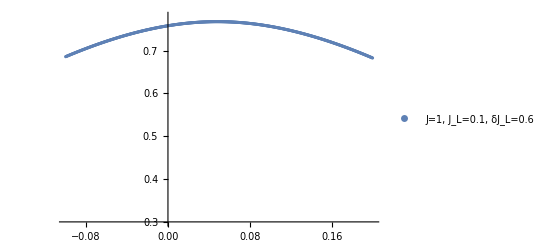

```mathematica
A =ListPlot[l[[2]],PlotRange->{0.3,0.78},PlotLegends->{"J=1, J_L=0.1, δJ_L=0.6"}]
```

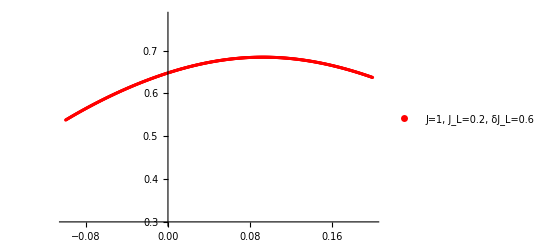

```mathematica
B = ListPlot[l[[4]],PlotRange->{0.3,0.78},PlotStyle->Red,PlotLegends->{"J=1, J_L=0.2, δJ_L=0.6"}]
```

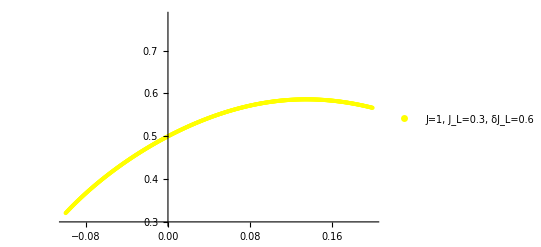

```mathematica
CC = ListPlot[l[[6]],PlotRange->{0.3,0.78},PlotStyle->Yellow,PlotLegends->{"J=1, J_L=0.3, δJ_L=0.6"}]
```

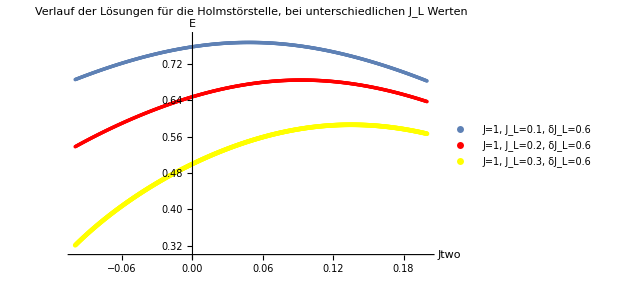

```mathematica
Show[A,B,CC,AxesLabel->{Jtwo,"E"},PlotLabel->"Verlauf der Lösungen für die Holmstörstelle, bei unterschiedlichen J_L Werten"]
```

Das ganze nochmal für Jone

```mathematica
ListerJone[Plusminus_,Xstart_,StartIteration_,Jtwoo_,p_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,Jtwoo,p,z],{z,StartIteration}]}}},
Do[
Jonee=Plusminus(n+1)*0.0005;
a=Check[FindRoot[NullsHolm[Jonee,Jtwoo,p,z]==0,{z,z/.lst[[n,2]]}],{z->0}]
;
AppendTo[lst,{Jonee,a}];
,{n,1,199,1}
];
lst
]
```

```mathematica
VerlaufJone[HowMany_,p_] := Module[{lst={}},
For[i=0,i<HowMany,i++,
AppendTo[lst,{1,i*0.1,p}];
AppendTo[lst,Fueger[moduler[ListerJone[-1,-0.0005,Zero[1,0,p],i*0.02,p]],moduler[ListerJone[1,0.0005,Zero[1,0,p],i*0.02,p]]]]
];
ll = lst
]
```

```mathematica
VerlaufJone[3,0.6]
```

{{1,0.,0.6},{{-0.0005,0.836958},{-0.001,0.837255},{-0.0015,0.837551},{-0.002,0.837846},{-0.0025,0.83814},{-0.003,0.838433},{-0.0035,0.838724},{-0.004,0.839015},{-0.0045,0.839304},{-0.005,0.839592},{-0.0055,0.839879},{-0.006,0.840165},{-0.0065,0.84045},{-0.007,0.840733},{-0.0075,0.841016},{-0.008,0.841297},{-0.0085,0.841577},{-0.009,0.841856},{-0.0095,0.842134},{-0.01,0.84241},{-0.0105,0.842686},{-0.011,0.84296},{-0.0115,0.843233},{-0.012,0.843505},{-0.0125,0.843775},{-0.013,0.844045},{-0.0135,0.844313},{-0.014,0.84458},{-0.0145,0.844845},{-0.015,0.84511},{-0.0155,0.845373},{-0.016,0.845635},{-0.0165,0.845896},{-0.017,0.846155},{-0.0175,0.846414},{-0.018,0.846671},{-0.0185,0.846926},{-0.019,0.847181},{-0.0195,0.847434},{-0.02,0.847686},{-0.0205,0.847937},{-0.021,0.848186},{-0.0215,0.848434},{-0.022,0.848681},{-0.0225,0.848926},{-0.023,0.84917},{-0.0235,0.849413},{-0.024,0.849655},{-0.0245,0.849895},{-0.025,0.850134},{-0.0255,0.850371},{-0.026,0.850607},{-0.0265,0.850842},{-0.027,0.851076},{-0.0275,0.851308},{-0.028,0.851538},{-0.0285,0.851768},{-0.029,0.851996},{-0.0295,0.852222},{-0.03,0.852447},{-0.0305,0.852671},{-0.031,0.852894},{-0.0315,0.853115},{-0.032,0.853334},{-0.0325,0.853552},{-0.033,0.853769},{-0.0335,0.853984},{-0.034,0.854198},{-0.0345,0.85441},{-0.035,0.854621},{-0.0355,0.854831},{-0.036,0.855039},{-0.0365,0.855245},{-0.037,0.85545},{-0.0375,0.855653},{-0.038,0.855855},{-0.0385,0.856056},{-0.039,0.856255},{-0.0395,0.856452},{-0.04,0.856648},{-0.0405,0.856843},{-0.041,0.857035},{-0.0415,0.857227},{-0.042,0.857416},{-0.0425,0.857604},{-0.043,0.857791},{-0.0435,0.857976},{-0.044,0.858159},{-0.0445,0.858341},{-0.045,0.858521},{-0.0455,0.8587},{-0.046,0.858877},{-0.0465,0.859052},{-0.047,0.859226},{-0.0475,0.859398},{-0.048,0.859568},{-0.0485,0.859737},{-0.049,0.859904},{-0.0495,0.860069},{-0.05,0.860233},{-0.0505,0.860394},{-0.051,0.860555},{-0.0515,0.860713},{-0.052,0.86087},{-0.0525,0.861025},{-0.053,0.861178},{-0.0535,0.861329},{-0.054,0.861479},{-0.0545,0.861627},{-0.055,0.861773},{-0.0555,0.861918},{-0.056,0.86206},{-0.0565,0.862201},{-0.057,0.86234},{-0.0575,0.862477},{-0.058,0.862612},{-0.0585,0.862745},{-0.059,0.862877},{-0.0595,0.863006},{-0.06,0.863134},{-0.0605,0.86326},{-0.061,0.863383},{-0.0615,0.863505},{-0.062,0.863625},{-0.0625,0.863743},{-0.063,0.863859},{-0.0635,0.863974},{-0.064,0.864086},{-0.0645,0.864196},{-0.065,0.864304},{-0.0655,0.86441},{-0.066,0.864514},{-0.0665,0.864616},{-0.067,0.864716},{-0.0675,0.864814},{-0.068,0.86491},{-0.0685,0.865004},{-0.069,0.865095},{-0.0695,0.865185},{-0.07,0.865272},{-0.0705,0.865357},{-0.071,0.86544},{-0.0715,0.865521},{-0.072,0.8656},{-0.0725,0.865676},{-0.073,0.865751},{-0.0735,0.865823},{-0.074,0.865893},{-0.0745,0.86596},{-0.075,0.866025},{-0.0755,0.866088},{-0.076,0.866149},{-0.0765,0.866208},{-0.077,0.866264},{-0.0775,0.866317},{-0.078,0.866369},{-0.0785,0.866418},{-0.079,0.866464},{-0.0795,0.866508},{-0.08,0.86655},{-0.0805,0.866589},{-0.081,0.866626},{-0.0815,0.866661},{-0.082,0.866693},{-0.0825,0.866722},{-0.083,0.866749},{-0.0835,0.866773},{-0.084,0.866795},{-0.0845,0.866814},{-0.085,0.866831},{-0.0855,0.866845},{-0.086,0.866856},{-0.0865,0.866865},{-0.087,0.866871},{-0.0875,0.866874},{-0.088,0.866875},{-0.0885,0.866873},{-0.089,0.866868},{-0.0895,0.86686},{-0.09,0.86685},{-0.0905,0.866837},{-0.091,0.866821},{-0.0915,0.866802},{-0.092,0.86678},{-0.0925,0.866755},{-0.093,0.866728},{-0.0935,0.866698},{-0.094,0.866664},{-0.0945,0.866628},{-0.095,0.866588},{-0.0955,0.866546},{-0.096,0.866501},{-0.0965,0.866452},{-0.097,0.866401},{-0.0975,0.866346},{-0.098,0.866288},{-0.0985,0.866227},{-0.099,0.866163},{-0.0995,0.866096},{-0.1,0.866025},{0.0005,0.836361},{0.001,0.83606},{0.0015,0.835759},{0.002,0.835456},{0.0025,0.835152},{0.003,0.834847},{0.0035,0.834542},{0.004,0.834235},{0.0045,0.833927},{0.005,0.833617},{0.0055,0.833307},{0.006,0.832996},{0.0065,0.832684},{0.007,0.83237},{0.0075,0.832056},{0.008,0.83174},{0.0085,0.831424},{0.009,0.831106},{0.0095,0.830788},{0.01,0.830468},{0.0105,0.830148},{0.011,0.829826},{0.0115,0.829503},{0.012,0.829179},{0.0125,0.828855},{0.013,0.828529},{0.0135,0.828202},{0.014,0.827874},{0.0145,0.827545},{0.015,0.827216},{0.0155,0.826885},{0.016,0.826553},{0.0165,0.82622},{0.017,0.825886},{0.0175,0.825552},{0.018,0.825216},{0.0185,0.824879},{0.019,0.824541},{0.0195,0.824203},{0.02,0.823863},{0.0205,0.823522},{0.021,0.823181},{0.0215,0.822838},{0.022,0.822494},{0.0225,0.82215},{0.023,0.821804},{0.0235,0.821458},{0.024,0.82111},{0.0245,0.820762},{0.025,0.820413},{0.0255,0.820062},{0.026,0.819711},{0.0265,0.819359},{0.027,0.819006},{0.0275,0.818652},{0.028,0.818297},{0.0285,0.817941},{0.029,0.817584},{0.0295,0.817226},{0.03,0.816868},{0.0305,0.816508},{0.031,0.816147},{0.0315,0.815786},{0.032,0.815424},{0.0325,0.81506},{0.033,0.814696},{0.0335,0.814331},{0.034,0.813965},{0.0345,0.813598},{0.035,0.81323},{0.0355,0.812861},{0.036,0.812492},{0.0365,0.812121},{0.037,0.81175},{0.0375,0.811377},{0.038,0.811004},{0.0385,0.81063},{0.039,0.810255},{0.0395,0.809879},{0.04,0.809502},{0.0405,0.809125},{0.041,0.808746},{0.0415,0.808367},{0.042,0.807986},{0.0425,0.807605},{0.043,0.807223},{0.0435,0.80684},{0.044,0.806457},{0.0445,0.806072},{0.045,0.805686},{0.0455,0.8053},{0.046,0.804913},{0.0465,0.804525},{0.047,0.804136},{0.0475,0.803746},{0.048,0.803355},{0.0485,0.802963},{0.049,0.802571},{0.0495,0.802178},{0.05,0.801784},{0.0505,0.801389},{0.051,0.800993},{0.0515,0.800596},{0.052,0.800199},{0.0525,0.799801},{0.053,0.799401},{0.0535,0.799001},{0.054,0.7986},{0.0545,0.798199},{0.055,0.797796},{0.0555,0.797393},{0.056,0.796989},{0.0565,0.796584},{0.057,0.796178},{0.0575,0.795771},{0.058,0.795364},{0.0585,0.794955},{0.059,0.794546},{0.0595,0.794136},{0.06,0.793725},{0.0605,0.793314},{0.061,0.792901},{0.0615,0.792488},{0.062,0.792074},{0.0625,0.791659},{0.063,0.791243},{0.0635,0.790827},{0.064,0.79041},{0.0645,0.789991},{0.065,0.789572},{0.0655,0.789153},{0.066,0.788732},{0.0665,0.788311},{0.067,0.787889},{0.0675,0.787466},{0.068,0.787042},{0.0685,0.786617},{0.069,0.786192},{0.0695,0.785766},{0.07,0.785339},{0.0705,0.784911},{0.071,0.784482},{0.0715,0.784053},{0.072,0.783623},{0.0725,0.783192},{0.073,0.78276},{0.0735,0.782327},{0.074,0.781894},{0.0745,0.78146},{0.075,0.781025},{0.0755,0.780589},{0.076,0.780153},{0.0765,0.779715},{0.077,0.779277},{0.0775,0.778838},{0.078,0.778399},{0.0785,0.777958},{0.079,0.777517},{0.0795,0.777075},{0.08,0.776632},{0.0805,0.776189},{0.081,0.775744},{0.0815,0.775299},{0.082,0.774853},{0.0825,0.774407},{0.083,0.773959},{0.0835,0.773511},{0.084,0.773062},{0.0845,0.772612},{0.085,0.772162},{0.0855,0.77171},{0.086,0.771258},{0.0865,0.770805},{0.087,0.770352},{0.0875,0.769897},{0.088,0.769442},{0.0885,0.768986},{0.089,0.768529},{0.0895,0.768072},{0.09,0.767614},{0.0905,0.767155},{0.091,0.766695},{0.0915,0.766234},{0.092,0.765773},{0.0925,0.765311},{0.093,0.764848},{0.0935,0.764384},{0.094,0.76392},{0.0945,0.763455},{0.095,0.762989},{0.0955,0.762522},{0.096,0.762055},{0.0965,0.761586},{0.097,0.761117},{0.0975,0.760648},{0.098,0.760177},{0.0985,0.759706},{0.099,0.759234},{0.0995,0.758761},{0.1,0.758288}},{1,0.1,0.6},{{-0.0005,0.835331},{-0.001,0.835589},{-0.0015,0.835847},{-0.002,0.836103},{-0.0025,0.836358},{-0.003,0.836612},{-0.0035,0.836864},{-0.004,0.837116},{-0.0045,0.837367},{-0.005,0.837616},{-0.0055,0.837865},{-0.006,0.838112},{-0.0065,0.838359},{-0.007,0.838604},{-0.0075,0.838848},{-0.008,0.839091},{-0.0085,0.839333},{-0.009,0.839574},{-0.0095,0.839814},{-0.01,0.840052},{-0.0105,0.84029},{-0.011,0.840526},{-0.0115,0.840761},{-0.012,0.840995},{-0.0125,0.841228},{-0.013,0.84146},{-0.0135,0.841691},{-0.014,0.84192},{-0.0145,0.842149},{-0.015,0.842376},{-0.0155,0.842602},{-0.016,0.842827},{-0.0165,0.843051},{-0.017,0.843273},{-0.0175,0.843495},{-0.018,0.843715},{-0.0185,0.843934},{-0.019,0.844152},{-0.0195,0.844369},{-0.02,0.844585},{-0.0205,0.844799},{-0.021,0.845012},{-0.0215,0.845224},{-0.022,0.845435},{-0.0225,0.845645},{-0.023,0.845853},{-0.0235,0.846061},{-0.024,0.846267},{-0.0245,0.846471},{-0.025,0.846675},{-0.0255,0.846877},{-0.026,0.847079},{-0.0265,0.847279},{-0.027,0.847477},{-0.0275,0.847675},{-0.028,0.847871},{-0.0285,0.848066},{-0.029,0.84826},{-0.0295,0.848452},{-0.03,0.848644},{-0.0305,0.848834},{-0.031,0.849022},{-0.0315,0.84921},{-0.032,0.849396},{-0.0325,0.849581},{-0.033,0.849765},{-0.0335,0.849947},{-0.034,0.850128},{-0.0345,0.850308},{-0.035,0.850487},{-0.0355,0.850664},{-0.036,0.85084},{-0.0365,0.851015},{-0.037,0.851188},{-0.0375,0.85136},{-0.038,0.851531},{-0.0385,0.8517},{-0.039,0.851868},{-0.0395,0.852035},{-0.04,0.852201},{-0.0405,0.852365},{-0.041,0.852527},{-0.0415,0.852689},{-0.042,0.852849},{-0.0425,0.853008},{-0.043,0.853165},{-0.0435,0.853321},{-0.044,0.853476},{-0.0445,0.853629},{-0.045,0.853781},{-0.0455,0.853931},{-0.046,0.85408},{-0.0465,0.854228},{-0.047,0.854374},{-0.0475,0.854519},{-0.048,0.854663},{-0.0485,0.854805},{-0.049,0.854946},{-0.0495,0.855085},{-0.05,0.855223},{-0.0505,0.855359},{-0.051,0.855494},{-0.0515,0.855628},{-0.052,0.85576},{-0.0525,0.855891},{-0.053,0.85602},{-0.0535,0.856148},{-0.054,0.856274},{-0.0545,0.856399},{-0.055,0.856523},{-0.0555,0.856645},{-0.056,0.856765},{-0.0565,0.856884},{-0.057,0.857002},{-0.0575,0.857118},{-0.058,0.857232},{-0.0585,0.857345},{-0.059,0.857457},{-0.0595,0.857567},{-0.06,0.857675},{-0.0605,0.857782},{-0.061,0.857888},{-0.0615,0.857991},{-0.062,0.858094},{-0.0625,0.858195},{-0.063,0.858294},{-0.0635,0.858391},{-0.064,0.858488},{-0.0645,0.858582},{-0.065,0.858675},{-0.0655,0.858766},{-0.066,0.858856},{-0.0665,0.858945},{-0.067,0.859031},{-0.0675,0.859116},{-0.068,0.8592},{-0.0685,0.859281},{-0.069,0.859362},{-0.0695,0.85944},{-0.07,0.859517},{-0.0705,0.859593},{-0.071,0.859666},{-0.0715,0.859738},{-0.072,0.859809},{-0.0725,0.859877},{-0.073,0.859944},{-0.0735,0.86001},{-0.074,0.860073},{-0.0745,0.860135},{-0.075,0.860196},{-0.0755,0.860254},{-0.076,0.860311},{-0.0765,0.860367},{-0.077,0.86042},{-0.0775,0.860472},{-0.078,0.860522},{-0.0785,0.86057},{-0.079,0.860617},{-0.0795,0.860662},{-0.08,0.860705},{-0.0805,0.860746},{-0.081,0.860786},{-0.0815,0.860824},{-0.082,0.86086},{-0.0825,0.860894},{-0.083,0.860926},{-0.0835,0.860957},{-0.084,0.860986},{-0.0845,0.861013},{-0.085,0.861038},{-0.0855,0.861062},{-0.086,0.861083},{-0.0865,0.861103},{-0.087,0.861121},{-0.0875,0.861137},{-0.088,0.861151},{-0.0885,0.861164},{-0.089,0.861174},{-0.0895,0.861183},{-0.09,0.861189},{-0.0905,0.861194},{-0.091,0.861197},{-0.0915,0.861198},{-0.092,0.861197},{-0.0925,0.861194},{-0.093,0.861189},{-0.0935,0.861183},{-0.094,0.861174},{-0.0945,0.861164},{-0.095,0.861151},{-0.0955,0.861136},{-0.096,0.86112},{-0.0965,0.861102},{-0.097,0.861081},{-0.0975,0.861059},{-0.098,0.861034},{-0.0985,0.861008},{-0.099,0.860979},{-0.0995,0.860949},{-0.1,0.860916},{0.0005,0.834812},{0.001,0.83455},{0.0015,0.834288},{0.002,0.834024},{0.0025,0.83376},{0.003,0.833494},{0.0035,0.833227},{0.004,0.83296},{0.0045,0.832691},{0.005,0.832421},{0.0055,0.83215},{0.006,0.831879},{0.0065,0.831606},{0.007,0.831332},{0.0075,0.831057},{0.008,0.830781},{0.0085,0.830504},{0.009,0.830226},{0.0095,0.829947},{0.01,0.829667},{0.0105,0.829386},{0.011,0.829104},{0.0115,0.828821},{0.012,0.828537},{0.0125,0.828252},{0.013,0.827966},{0.0135,0.827679},{0.014,0.827391},{0.0145,0.827102},{0.015,0.826812},{0.0155,0.826521},{0.016,0.826229},{0.0165,0.825936},{0.017,0.825642},{0.0175,0.825347},{0.018,0.825051},{0.0185,0.824754},{0.019,0.824456},{0.0195,0.824157},{0.02,0.823858},{0.0205,0.823557},{0.021,0.823255},{0.0215,0.822952},{0.022,0.822649},{0.0225,0.822344},{0.023,0.822039},{0.0235,0.821732},{0.024,0.821425},{0.0245,0.821116},{0.025,0.820807},{0.0255,0.820497},{0.026,0.820185},{0.0265,0.819873},{0.027,0.81956},{0.0275,0.819246},{0.028,0.818931},{0.0285,0.818615},{0.029,0.818298},{0.0295,0.81798},{0.03,0.817662},{0.0305,0.817342},{0.031,0.817022},{0.0315,0.8167},{0.032,0.816378},{0.0325,0.816054},{0.033,0.81573},{0.0335,0.815405},{0.034,0.815079},{0.0345,0.814752},{0.035,0.814424},{0.0355,0.814095},{0.036,0.813765},{0.0365,0.813435},{0.037,0.813103},{0.0375,0.812771},{0.038,0.812438},{0.0385,0.812103},{0.039,0.811768},{0.0395,0.811432},{0.04,0.811095},{0.0405,0.810757},{0.041,0.810419},{0.0415,0.810079},{0.042,0.809739},{0.0425,0.809397},{0.043,0.809055},{0.0435,0.808712},{0.044,0.808368},{0.0445,0.808023},{0.045,0.807677},{0.0455,0.807331},{0.046,0.806983},{0.0465,0.806635},{0.047,0.806286},{0.0475,0.805935},{0.048,0.805584},{0.0485,0.805233},{0.049,0.80488},{0.0495,0.804526},{0.05,0.804172},{0.0505,0.803817},{0.051,0.80346},{0.0515,0.803103},{0.052,0.802745},{0.0525,0.802387},{0.053,0.802027},{0.0535,0.801667},{0.054,0.801305},{0.0545,0.800943},{0.055,0.80058},{0.0555,0.800216},{0.056,0.799852},{0.0565,0.799486},{0.057,0.79912},{0.0575,0.798752},{0.058,0.798384},{0.0585,0.798015},{0.059,0.797646},{0.0595,0.797275},{0.06,0.796903},{0.0605,0.796531},{0.061,0.796158},{0.0615,0.795784},{0.062,0.795409},{0.0625,0.795034},{0.063,0.794657},{0.0635,0.79428},{0.064,0.793902},{0.0645,0.793523},{0.065,0.793143},{0.0655,0.792763},{0.066,0.792381},{0.0665,0.791999},{0.067,0.791616},{0.0675,0.791232},{0.068,0.790847},{0.0685,0.790462},{0.069,0.790075},{0.0695,0.789688},{0.07,0.7893},{0.0705,0.788911},{0.071,0.788522},{0.0715,0.788131},{0.072,0.78774},{0.0725,0.787348},{0.073,0.786955},{0.0735,0.786562},{0.074,0.786167},{0.0745,0.785772},{0.075,0.785376},{0.0755,0.784979},{0.076,0.784581},{0.0765,0.784183},{0.077,0.783783},{0.0775,0.783383},{0.078,0.782982},{0.0785,0.78258},{0.079,0.782178},{0.0795,0.781775},{0.08,0.781371},{0.0805,0.780966},{0.081,0.78056},{0.0815,0.780153},{0.082,0.779746},{0.0825,0.779338},{0.083,0.778929},{0.0835,0.778519},{0.084,0.778109},{0.0845,0.777698},{0.085,0.777286},{0.0855,0.776873},{0.086,0.776459},{0.0865,0.776045},{0.087,0.775629},{0.0875,0.775213},{0.088,0.774797},{0.0885,0.774379},{0.089,0.773961},{0.0895,0.773541},{0.09,0.773121},{0.0905,0.772701},{0.091,0.772279},{0.0915,0.771857},{0.092,0.771434},{0.0925,0.77101},{0.093,0.770585},{0.0935,0.77016},{0.094,0.769734},{0.0945,0.769307},{0.095,0.768879},{0.0955,0.76845},{0.096,0.768021},{0.0965,0.767591},{0.097,0.76716},{0.0975,0.766728},{0.098,0.766296},{0.0985,0.765863},{0.099,0.765429},{0.0995,0.764994},{0.1,0.764559}},{1,0.2,0.6},{{-0.0005,0.830594},{-0.001,0.830816},{-0.0015,0.831037},{-0.002,0.831257},{-0.0025,0.831476},{-0.003,0.831694},{-0.0035,0.831911},{-0.004,0.832127},{-0.0045,0.832342},{-0.005,0.832556},{-0.0055,0.832769},{-0.006,0.832981},{-0.0065,0.833192},{-0.007,0.833402},{-0.0075,0.833611},{-0.008,0.833818},{-0.0085,0.834025},{-0.009,0.834231},{-0.0095,0.834436},{-0.01,0.834639},{-0.0105,0.834842},{-0.011,0.835044},{-0.0115,0.835244},{-0.012,0.835444},{-0.0125,0.835642},{-0.013,0.83584},{-0.0135,0.836036},{-0.014,0.836232},{-0.0145,0.836426},{-0.015,0.836619},{-0.0155,0.836811},{-0.016,0.837002},{-0.0165,0.837193},{-0.017,0.837382},{-0.0175,0.83757},{-0.018,0.837757},{-0.0185,0.837942},{-0.019,0.838127},{-0.0195,0.838311},{-0.02,0.838494},{-0.0205,0.838675},{-0.021,0.838856},{-0.0215,0.839035},{-0.022,0.839213},{-0.0225,0.839391},{-0.023,0.839567},{-0.0235,0.839742},{-0.024,0.839916},{-0.0245,0.840089},{-0.025,0.840261},{-0.0255,0.840431},{-0.026,0.840601},{-0.0265,0.84077},{-0.027,0.840937},{-0.0275,0.841103},{-0.028,0.841269},{-0.0285,0.841433},{-0.029,0.841596},{-0.0295,0.841758},{-0.03,0.841918},{-0.0305,0.842078},{-0.031,0.842237},{-0.0315,0.842394},{-0.032,0.84255},{-0.0325,0.842705},{-0.033,0.84286},{-0.0335,0.843012},{-0.034,0.843164},{-0.0345,0.843315},{-0.035,0.843464},{-0.0355,0.843613},{-0.036,0.84376},{-0.0365,0.843906},{-0.037,0.844051},{-0.0375,0.844195},{-0.038,0.844338},{-0.0385,0.844479},{-0.039,0.84462},{-0.0395,0.844759},{-0.04,0.844897},{-0.0405,0.845034},{-0.041,0.845169},{-0.0415,0.845304},{-0.042,0.845437},{-0.0425,0.84557},{-0.043,0.845701},{-0.0435,0.845831},{-0.044,0.845959},{-0.0445,0.846087},{-0.045,0.846213},{-0.0455,0.846338},{-0.046,0.846462},{-0.0465,0.846585},{-0.047,0.846707},{-0.0475,0.846827},{-0.048,0.846946},{-0.0485,0.847064},{-0.049,0.847181},{-0.0495,0.847296},{-0.05,0.847411},{-0.0505,0.847524},{-0.051,0.847636},{-0.0515,0.847747},{-0.052,0.847856},{-0.0525,0.847965},{-0.053,0.848072},{-0.0535,0.848178},{-0.054,0.848282},{-0.0545,0.848386},{-0.055,0.848488},{-0.0555,0.848589},{-0.056,0.848688},{-0.0565,0.848787},{-0.057,0.848884},{-0.0575,0.84898},{-0.058,0.849075},{-0.0585,0.849168},{-0.059,0.849261},{-0.0595,0.849352},{-0.06,0.849441},{-0.0605,0.84953},{-0.061,0.849617},{-0.0615,0.849703},{-0.062,0.849788},{-0.0625,0.849871},{-0.063,0.849953},{-0.0635,0.850034},{-0.064,0.850114},{-0.0645,0.850192},{-0.065,0.850269},{-0.0655,0.850345},{-0.066,0.850419},{-0.0665,0.850492},{-0.067,0.850564},{-0.0675,0.850635},{-0.068,0.850704},{-0.0685,0.850772},{-0.069,0.850839},{-0.0695,0.850904},{-0.07,0.850968},{-0.0705,0.851031},{-0.071,0.851092},{-0.0715,0.851152},{-0.072,0.851211},{-0.0725,0.851268},{-0.073,0.851325},{-0.0735,0.851379},{-0.074,0.851433},{-0.0745,0.851485},{-0.075,0.851536},{-0.0755,0.851585},{-0.076,0.851633},{-0.0765,0.85168},{-0.077,0.851725},{-0.0775,0.851769},{-0.078,0.851812},{-0.0785,0.851853},{-0.079,0.851893},{-0.0795,0.851932},{-0.08,0.851969},{-0.0805,0.852005},{-0.081,0.85204},{-0.0815,0.852073},{-0.082,0.852104},{-0.0825,0.852135},{-0.083,0.852164},{-0.0835,0.852191},{-0.084,0.852218},{-0.0845,0.852242},{-0.085,0.852266},{-0.0855,0.852288},{-0.086,0.852308},{-0.0865,0.852328},{-0.087,0.852345},{-0.0875,0.852362},{-0.088,0.852377},{-0.0885,0.85239},{-0.089,0.852402},{-0.0895,0.852413},{-0.09,0.852422},{-0.0905,0.85243},{-0.091,0.852437},{-0.0915,0.852442},{-0.092,0.852445},{-0.0925,0.852447},{-0.093,0.852448},{-0.0935,0.852447},{-0.094,0.852445},{-0.0945,0.852441},{-0.095,0.852436},{-0.0955,0.852429},{-0.096,0.852421},{-0.0965,0.852412},{-0.097,0.852401},{-0.0975,0.852388},{-0.098,0.852374},{-0.0985,0.852359},{-0.099,0.852342},{-0.0995,0.852323},{-0.1,0.852304},{0.0005,0.830147},{0.001,0.829922},{0.0015,0.829696},{0.002,0.829469},{0.0025,0.829241},{0.003,0.829012},{0.0035,0.828782},{0.004,0.828552},{0.0045,0.82832},{0.005,0.828087},{0.0055,0.827853},{0.006,0.827618},{0.0065,0.827382},{0.007,0.827145},{0.0075,0.826908},{0.008,0.826669},{0.0085,0.826429},{0.009,0.826188},{0.0095,0.825947},{0.01,0.825704},{0.0105,0.825461},{0.011,0.825216},{0.0115,0.824971},{0.012,0.824724},{0.0125,0.824477},{0.013,0.824228},{0.0135,0.823979},{0.014,0.823729},{0.0145,0.823477},{0.015,0.823225},{0.0155,0.822972},{0.016,0.822718},{0.0165,0.822463},{0.017,0.822207},{0.0175,0.82195},{0.018,0.821692},{0.0185,0.821433},{0.019,0.821174},{0.0195,0.820913},{0.02,0.820651},{0.0205,0.820389},{0.021,0.820125},{0.0215,0.819861},{0.022,0.819596},{0.0225,0.819329},{0.023,0.819062},{0.0235,0.818794},{0.024,0.818525},{0.0245,0.818255},{0.025,0.817984},{0.0255,0.817712},{0.026,0.81744},{0.0265,0.817166},{0.027,0.816891},{0.0275,0.816616},{0.028,0.81634},{0.0285,0.816062},{0.029,0.815784},{0.0295,0.815505},{0.03,0.815225},{0.0305,0.814944},{0.031,0.814662},{0.0315,0.81438},{0.032,0.814096},{0.0325,0.813812},{0.033,0.813526},{0.0335,0.81324},{0.034,0.812953},{0.0345,0.812665},{0.035,0.812376},{0.0355,0.812086},{0.036,0.811795},{0.0365,0.811503},{0.037,0.811211},{0.0375,0.810917},{0.038,0.810623},{0.0385,0.810328},{0.039,0.810032},{0.0395,0.809735},{0.04,0.809437},{0.0405,0.809138},{0.041,0.808838},{0.0415,0.808538},{0.042,0.808237},{0.0425,0.807934},{0.043,0.807631},{0.0435,0.807327},{0.044,0.807022},{0.0445,0.806717},{0.045,0.80641},{0.0455,0.806103},{0.046,0.805794},{0.0465,0.805485},{0.047,0.805175},{0.0475,0.804864},{0.048,0.804552},{0.0485,0.80424},{0.049,0.803926},{0.0495,0.803612},{0.05,0.803296},{0.0505,0.80298},{0.051,0.802663},{0.0515,0.802346},{0.052,0.802027},{0.0525,0.801708},{0.053,0.801387},{0.0535,0.801066},{0.054,0.800744},{0.0545,0.800421},{0.055,0.800097},{0.0555,0.799773},{0.056,0.799447},{0.0565,0.799121},{0.057,0.798794},{0.0575,0.798466},{0.058,0.798137},{0.0585,0.797807},{0.059,0.797477},{0.0595,0.797145},{0.06,0.796813},{0.0605,0.79648},{0.061,0.796146},{0.0615,0.795812},{0.062,0.795476},{0.0625,0.79514},{0.063,0.794803},{0.0635,0.794465},{0.064,0.794126},{0.0645,0.793786},{0.065,0.793446},{0.0655,0.793104},{0.066,0.792762},{0.0665,0.792419},{0.067,0.792075},{0.0675,0.791731},{0.068,0.791385},{0.0685,0.791039},{0.069,0.790692},{0.0695,0.790344},{0.07,0.789995},{0.0705,0.789646},{0.071,0.789295},{0.0715,0.788944},{0.072,0.788592},{0.0725,0.788239},{0.073,0.787886},{0.0735,0.787531},{0.074,0.787176},{0.0745,0.78682},{0.075,0.786463},{0.0755,0.786105},{0.076,0.785747},{0.0765,0.785387},{0.077,0.785027},{0.0775,0.784666},{0.078,0.784304},{0.0785,0.783942},{0.079,0.783579},{0.0795,0.783214},{0.08,0.782849},{0.0805,0.782484},{0.081,0.782117},{0.0815,0.78175},{0.082,0.781381},{0.0825,0.781012},{0.083,0.780643},{0.0835,0.780272},{0.084,0.779901},{0.0845,0.779528},{0.085,0.779155},{0.0855,0.778782},{0.086,0.778407},{0.0865,0.778032},{0.087,0.777655},{0.0875,0.777278},{0.088,0.776901},{0.0885,0.776522},{0.089,0.776143},{0.0895,0.775762},{0.09,0.775382},{0.0905,0.775},{0.091,0.774617},{0.0915,0.774234},{0.092,0.77385},{0.0925,0.773465},{0.093,0.773079},{0.0935,0.772693},{0.094,0.772305},{0.0945,0.771917},{0.095,0.771528},{0.0955,0.771139},{0.096,0.770748},{0.0965,0.770357},{0.097,0.769965},{0.0975,0.769572},{0.098,0.769179},{0.0985,0.768784},{0.099,0.768389},{0.0995,0.767993},{0.1,0.767597}}}

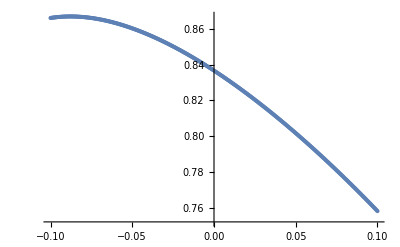

```mathematica
ABC = ListPlot[ll[[2]]]
```

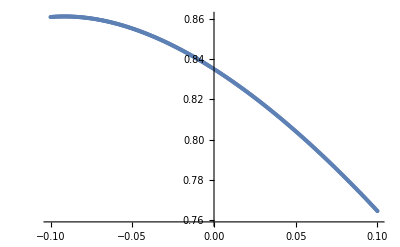

```mathematica
Easy = ListPlot[ll[[4]]]
```

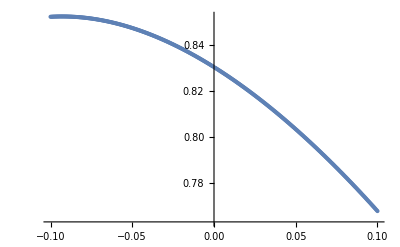

```mathematica
As123 = ListPlot[ll[[6]]]
```

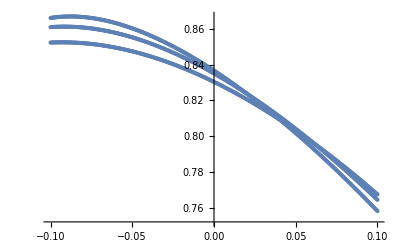

```mathematica
Show[ABC,Easy,As123]
```